# Combine plots of SFOPT with Scalar Extension

```mathematica
ClearAll["Global`*"]
```

```mathematica
myTicks[lower_,upper_,step_]:=Flatten[Module[{Local=#,LocalTicks},LocalTicks=Log[10,Range[10^(#-1),10^#,(10^#-10^(#-1))/(10-1)]];
Join[{#,""}&/@Most[LocalTicks],{{Last[LocalTicks],Which[Last[LocalTicks]==0,1,Last[LocalTicks]==1,10,True,Power[10,ToString[Last[LocalTicks]]]],{0.03,0}(*longer ticks*)}}]]&/@Range[lower,upper,step],1];
```

```mathematica
cleanRegionPlot[cp_Graphics]:=Module[{points,groups,regions,lines},groups=Cases[cp,{style__,g_GraphicsGroup}:>{{style},g},Infinity];
points=First@Cases[cp,GraphicsComplex[pts_,___]:>pts,Infinity];
regions=Table[Module[{group,style,polys,edges,cover,graph},{style,group}=g;
polys=Join@@Cases[group,Polygon[pt_,___]:>pt,Infinity];
edges=Join@@(Partition[#,2,1,1]&/@polys);
cover=Cases[Tally[Sort/@edges],{e_,1}:>e];
graph=Graph[UndirectedEdge@@@cover];
{Sequence@@style,FilledCurve[List/@Line/@First/@Map[First,FindEulerianCycle/@(Subgraph[graph,#]&)/@ConnectedComponents[graph],{3}]]}],{g,groups}];
lines=Cases[cp,{__,_Line},Infinity];(*only change*)Graphics[GraphicsComplex[points,{regions,lines}],Sequence@@Options[cp]]];
```

## SFOPT bound for v_R=20 TeV

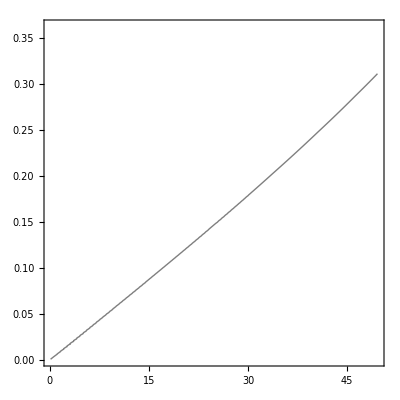

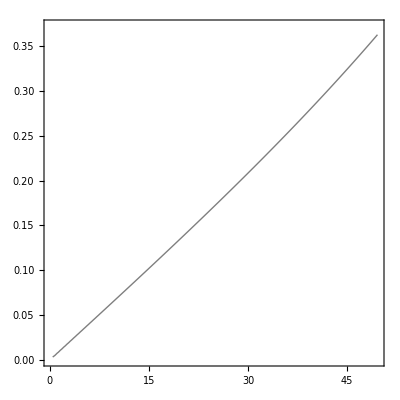

InterpolatingFunction[…][mS]

InterpolatingFunction[…][mS]

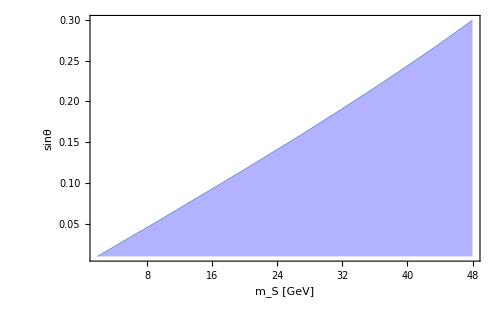

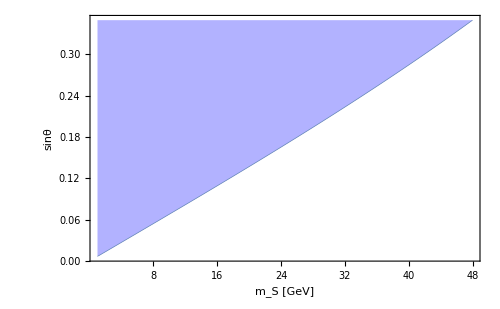

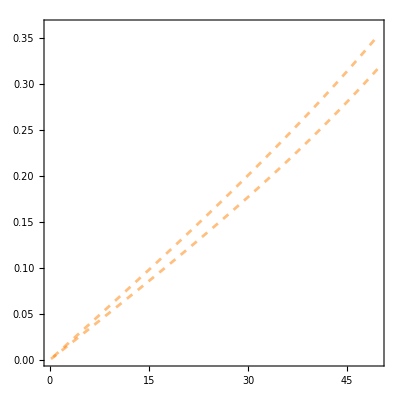

```mathematica
GeVdata‵20=Import[NotebookDirectory[]<>"GeV-SFOPTbound-20TeV.csv"];
strengthdata={#1,#2,#3}&@@@Select[GeVdata‵20,#[[3]]>0.5&&#[[4]]>0 &];
stabilitydata={#1,#2,#4}&@@@GeVdata‵20;
finetunedata={#1,#2,#4/#5}&@@@Select[GeVdata‵20,#[[3]]>0.5&&#[[4]]>0 &];
GeVSFOPT=ListContourPlot[strengthdata,Contours->{1},ContourShading->None,PlotRange->Full]
stability=ListContourPlot[stabilitydata,Contours->{0},ContourShading->None,PlotRange->Full]
SFOPTbound=Cases[Normal@GeVSFOPT, Line[x_] :> x, Infinity];
SFOPTboundfunc[mS_]=Interpolation[SFOPTbound[[1]],InterpolationOrder->2][mS]
stabilitybound=Cases[Normal@stability,Line[x_]:> x, Infinity];
stabilityboundfunc[mS_]=Interpolation[stabilitybound[[1]],InterpolationOrder->1][mS]
GeVSFOPTplot‵20=Plot[SFOPTboundfunc[mS],{mS,1.9,48},Filling->Bottom,BaseStyle->{FontSize->18,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->18],PlotRangePadding->None,ImageSize->500,PlotStyle->Directive[Thickness[0.001]],FillingStyle->Directive[Blue,Opacity[0.3]]]
GeVstabilityplot‵20=Plot[stabilityboundfunc[mS],{mS,1.,48},Filling->Top,BaseStyle->{FontSize->18,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->18],PlotRangePadding->None,ImageSize->500,PlotStyle->Directive[Thickness[0.001]],FillingStyle->Directive[Blue,Opacity[0.3]]]
finetune20=ListContourPlot[finetunedata,Contours->{0.05,0.2},ContourStyle->Directive[Dashed,Orange,Thickness[0.005]],ContourShading->None]
```

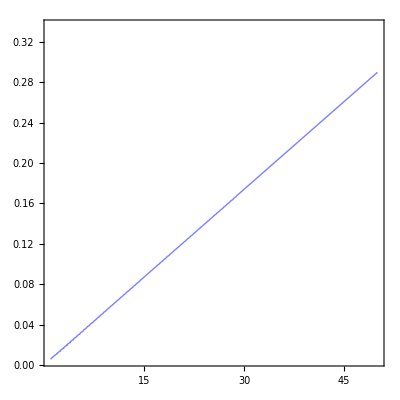

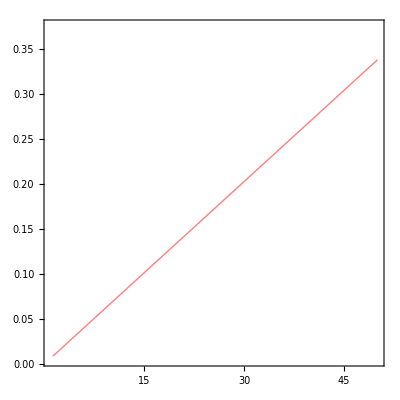

InterpolatingFunction[…][mS]

InterpolatingFunction[…][mS]

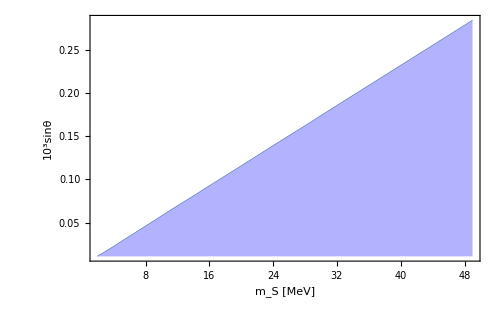

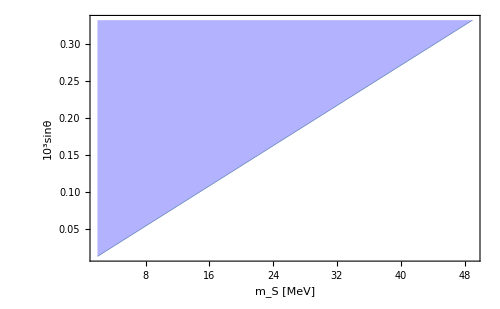

```mathematica
MeVdata‵20={#1*1000,1000*#2,#3,#4}&@@@Import[NotebookDirectory[]<>"MeV-SFOPTbound-20TeV.csv"];
strengthdata={#1,#2,#3}&@@@Select[MeVdata‵20,#[[3]]>0.5&&#[[4]]>0 &];
stabilitydata={#1,#2,#4}&@@@MeVdata‵20;
MeVSFOPT=ListContourPlot[strengthdata,Contours->{1},ContourShading->None,PlotRange->Full,ContourStyle->Blue]
stability=ListContourPlot[stabilitydata,Contours->{0},ContourShading->None,PlotRange->Full,ContourStyle->Red]
SFOPTbound=Cases[Normal@MeVSFOPT, Line[x_] :> x, Infinity];
SFOPTboundfunc[mS_]=Interpolation[SFOPTbound[[1]],InterpolationOrder->1][mS]
stabilitybound=Cases[Normal@stability,Line[x_]:> x, Infinity];
stabilityboundfunc[mS_]=Interpolation[stabilitybound[[1]],InterpolationOrder->1][mS]
MeVSFOPTplot‵20=Plot[SFOPTboundfunc[mS],{mS,1.96,49},BaseStyle->{FontSize->18,FontFamily->"Times"},Frame->True,Filling->Bottom,FrameLabel->{Style["m_S [MeV]",FontFamily->"Times",FontSize->18],Style["10^3sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->18],PlotRangePadding->None,ImageSize->500,PlotStyle->Directive[Thickness[0.001]],FillingStyle->Directive[Blue,Opacity[0.3]]]
MeVstabilityplot‵20=Plot[stabilityboundfunc[mS],{mS,1.96,49},Filling->Top,BaseStyle->{FontSize->18,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S [MeV]",FontFamily->"Times",FontSize->18],Style["10^3sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->18],PlotRangePadding->None,ImageSize->500,PlotStyle->Directive[Thickness[0.001]],FillingStyle->Directive[Blue,Opacity[0.3]]]
```

## v_R=10^5 GeV

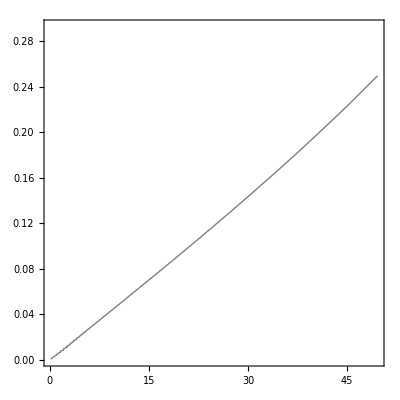

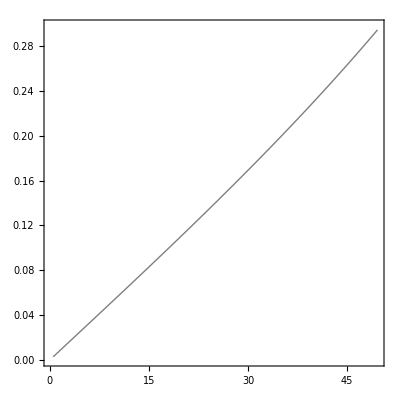

InterpolatingFunction[…][mS]

InterpolatingFunction[…][mS]

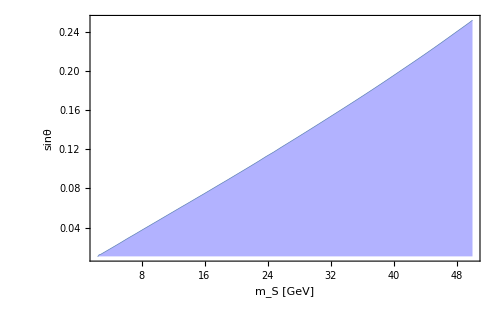

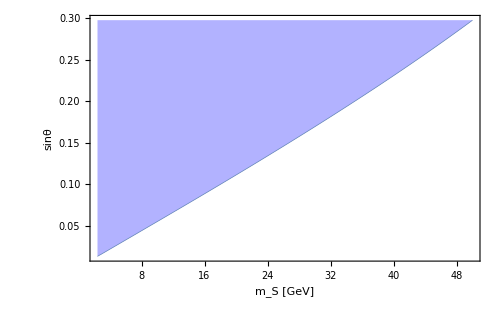

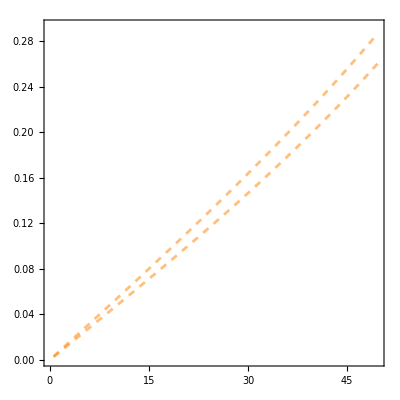

```mathematica
GeVdata‵5=Import[NotebookDirectory[]<>"GeV-SFOPTbound-10^5GeV.csv"];
strengthdata={#1,#2,#3}&@@@Select[GeVdata‵5,#[[3]]>0.5&&#[[4]]>0 &];
stabilitydata={#1,#2,#4}&@@@GeVdata‵5;
finetunedata={#1,#2,#4/#5}&@@@Select[GeVdata‵5,#[[3]]>0.5&&#[[4]]>0 &];
GeVSFOPT=ListContourPlot[strengthdata,Contours->{1},ContourShading->None,PlotRange->Full]
stability=ListContourPlot[stabilitydata,Contours->{0},ContourShading->None,PlotRange->Full]
SFOPTbound=Cases[Normal@GeVSFOPT, Line[x_] :> x, Infinity];
SFOPTboundfunc[mS_]=Interpolation[SFOPTbound[[1]],InterpolationOrder->1][mS]
stabilitybound=Cases[Normal@stability,Line[x_]:> x, Infinity];
stabilityboundfunc[mS_]=Interpolation[stabilitybound[[1]],InterpolationOrder->2][mS]
GeVSFOPTplot‵5=Plot[SFOPTboundfunc[mS],{mS,2.414,50},Filling->Bottom,BaseStyle->{FontSize->18,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->18],PlotRangePadding->None,ImageSize->500,PlotStyle->Directive[Thickness[0.001]],FillingStyle->Directive[Blue,Opacity[0.3]]]
GeVstabilityplot‵5=Plot[stabilityboundfunc[mS],{mS,2.414,50},Filling->Top,BaseStyle->{FontSize->18,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->18],PlotRangePadding->None,ImageSize->500,PlotStyle->Directive[Thickness[0.001]],FillingStyle->Directive[Blue,Opacity[0.3]]]
finetune5=ListContourPlot[finetunedata,Contours->{0.05,0.2},ContourStyle->Directive[Dashed,Orange,Thickness[0.005]],ContourShading->None]
```

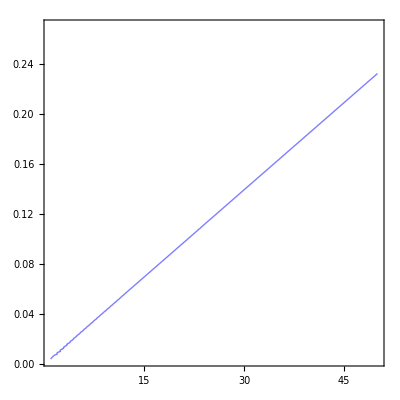

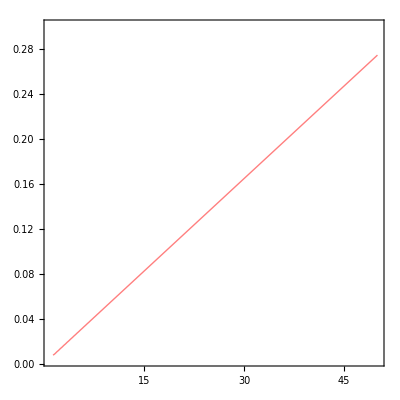

InterpolatingFunction[…][mS]

InterpolatingFunction[…][mS]

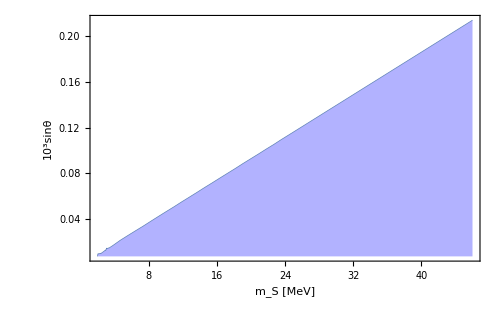

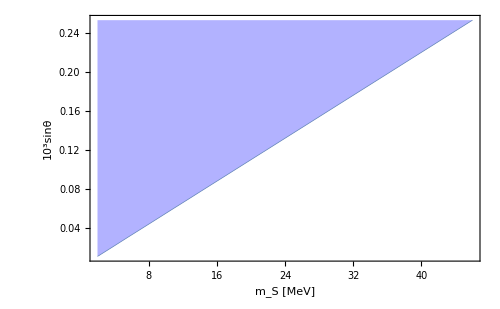

```mathematica
MeVdata‵5={#1*1000,1000*#2,#3,#4}&@@@Import[NotebookDirectory[]<>"MeV-SFOPTbound-10^5GeV.csv"];
strengthdata={#1,#2,#3}&@@@Select[MeVdata‵5,#[[3]]>0.5&&#[[4]]>0 &];
stabilitydata={#1,#2,#4}&@@@MeVdata‵5;
MeVSFOPT=ListContourPlot[strengthdata,Contours->{1},ContourShading->None,PlotRange->Full,ContourStyle->Blue]
stability=ListContourPlot[stabilitydata,Contours->{0},ContourShading->None,PlotRange->Full,ContourStyle->Red]
SFOPTbound=Cases[Normal@MeVSFOPT, Line[x_] :> x, Infinity];
SFOPTboundfunc[mS_]=Interpolation[SFOPTbound[[1]],InterpolationOrder->2][mS]
stabilitybound=Cases[Normal@stability,Line[x_]:> x, Infinity];
stabilityboundfunc[mS_]=Interpolation[stabilitybound[[1]],InterpolationOrder->2][mS]
MeVSFOPTplot‵5=Plot[SFOPTboundfunc[mS],{mS,1.96,46},BaseStyle->{FontSize->18,FontFamily->"Times"},Frame->True,Filling->Bottom,FrameLabel->{Style["m_S [MeV]",FontFamily->"Times",FontSize->18],Style["10^3sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->18],PlotRangePadding->None,ImageSize->500,PlotStyle->Directive[Thickness[0.001]],FillingStyle->Directive[Blue,Opacity[0.3]]]
MeVstabilityplot‵5=Plot[stabilityboundfunc[mS],{mS,1.96,46},Filling->Top,BaseStyle->{FontSize->18,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S [MeV]",FontFamily->"Times",FontSize->18],Style["10^3sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->18],PlotRangePadding->None,ImageSize->500,PlotStyle->Directive[Thickness[0.001]],FillingStyle->Directive[Blue,Opacity[0.3]]]
```

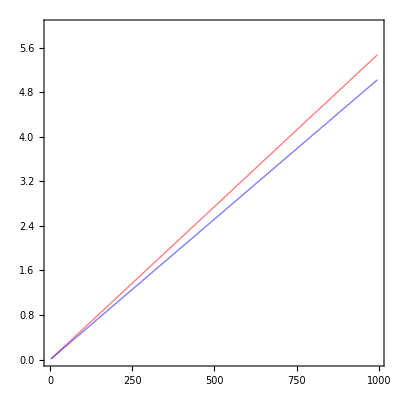

```mathematica
Show[{stability,MeVSFOPT}]
```

## LEP Probes

### 1996 Data

Model-independent production channel.

InterpolatingFunction[…][mS]

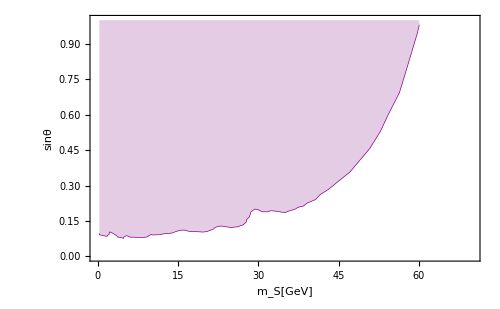

```mathematica
LEP1996data={#1,√#2}&@@@Import[NotebookDirectory[]<>"LEP1996.csv"];
LEP1996func[mS_]=Interpolation[LEP1996data,InterpolationOrder->1][mS]
LEP1996=ListLinePlot[LEP1996data,Filling->Top,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S[GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotRangePadding->None,ImageSize->500,PlotStyle->Directive[Purple,Thickness[0.001]],PlotRange->{{0,70},{0,1}},FillingStyle->Opacity[0.2]]
```

### 2003 ALEPH

Model-dependent, depending on the decay channel. The main contribution is from the bb decay.

```mathematica
mb=4.19;
mc=1.27;
mτ=1.78;
bBR[mS_]:=(3 mb^2 Re[(mS^2-4 mb^2)^(3/2)])/(3 mb^2 Re[(mS^2-4 mb^2)^(3/2)]+3 mc^2 Re[(mS^2-4 mc^2)^(3/2)]+mτ^2 Re[(mS^2-4 mτ^2)^(3/2)]);
cBR[mS_]:=(3 mc^2 Re[(mS^2-4 mc^2)^(3/2)])/(3 mb^2 Re[(mS^2-4 mb^2)^(3/2)]+3 mc^2 Re[(mS^2-4 mc^2)^(3/2)]+mτ^2 Re[(mS^2-4 mτ^2)^(3/2)]);τBR[mS_]:=(mτ^2 Re[(mS^2-4 mτ^2)^(3/2)])/(3 mb^2 Re[(mS^2-4 mb^2)^(3/2)]+3 mc^2 Re[(mS^2-4 mc^2)^(3/2)]+mτ^2 Re[(mS^2-4 mτ^2)^(3/2)]);
bblimit[mS_]=Interpolation[Import[NotebookDirectory[]<>"LEP-ALEPH.csv"],InterpolationOrder->1][mS]
```

InterpolatingFunction[…][mS]

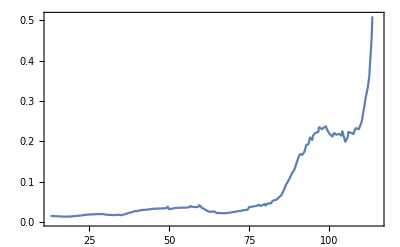

```mathematica
Plot[bblimit[mS],{mS,13,115}]
```

```mathematica
bb‵bound[mS_/;mS>=12.4]=√(bblimit[ mS]/bBR[mS]);
```

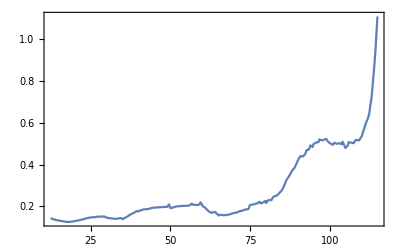

```mathematica
Plot[bb‵bound[mS],{mS,12.4,115}]
```

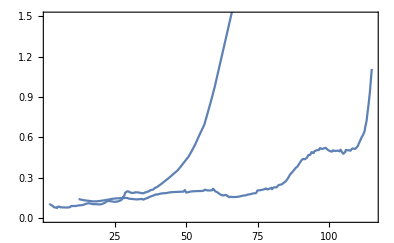

```mathematica
Show[{Plot[LEP1996func[mS],{mS,2.2,68.1}],Plot[bb‵bound[mS],{mS,12.4,115}]},PlotRange->{{2.3,115},{0,1.5}}]
```

```mathematica
Combinebound[mS_/;12.4<=mS<=68.1]:=Min[LEP1996func[mS],bb‵bound[mS]]
Combinebound[mS_/;mS<12.4]:=LEP1996func[mS]
Combinebound[mS_/;mS>68.1]:=bb‵bound[mS]
```

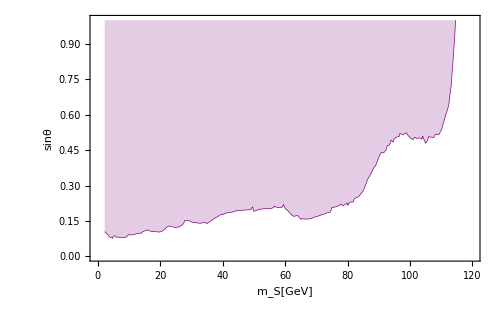

```mathematica
LEP=Plot[Combinebound[mS],{mS,2.3,115},Filling->Top,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S[GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotRangePadding->None,ImageSize->500,PlotStyle->Directive[Purple,Thickness[0.001]],PlotRange->{{0,120},{0,1}},FillingStyle->Opacity[0.2]]
```

## LHCb

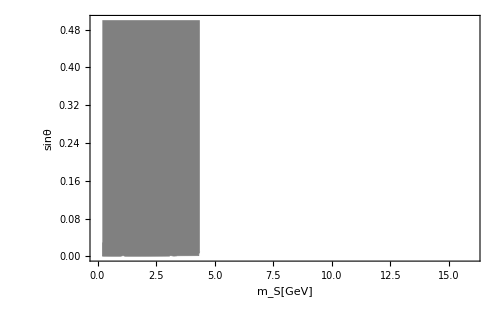

```mathematica
LHCbdata={#1, √#2}& @@@Import[NotebookDirectory[]<>"LHCb.csv"];
LHCb=ListLinePlot[LHCbdata,Filling->Top,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S[GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotRangePadding->None,ImageSize->500,PlotStyle->Directive[Gray,Thickness[0.001]],PlotRange->{{0,16},{0,0.5}},FillingStyle->Opacity[1]]
```

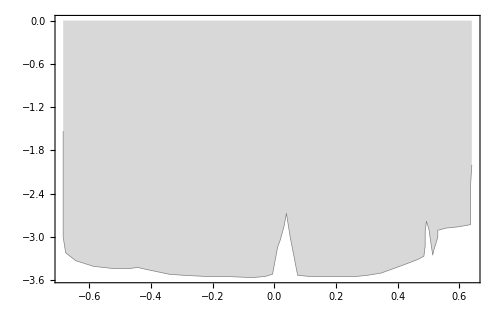

```mathematica
LHCbMeV={Log10[#1],Log10[#2]}&@@@LHCbdata;
LHCbMeVPlot=ListLinePlot[LHCbMeV,PlotStyle->Directive[Gray,Thickness[0.001]],Filling->Top,FillingStyle->Opacity[0.3]]
```

## NA62 & E949

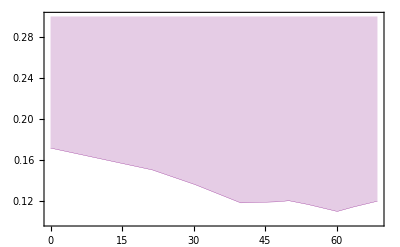

```mathematica
NA621={#1,1000*√(#2/(1.7*10^-3))}& @@@Import[NotebookDirectory[]<>"NA62-1.csv"];
NA62Plot1=ListLinePlot[NA621,PlotStyle->Directive[Purple,Thickness[0.0005]],Filling->Top,PlotRange->{Automatic,{0.1,0.3}}]
```

## SN

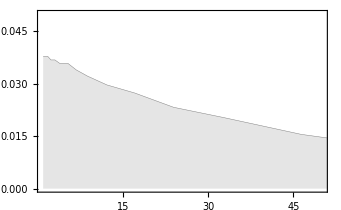

```mathematica
SNdata={#1,1000*#2}&@@@Import[NotebookDirectory[]<>"SN.csv"];
SN=ListLinePlot[SNdata,Filling->Bottom,PlotStyle->{Directive[Thickness[0.001],Gray]},PlotRange->{{1,50},{0.00,0.05}}]
```

## Planck

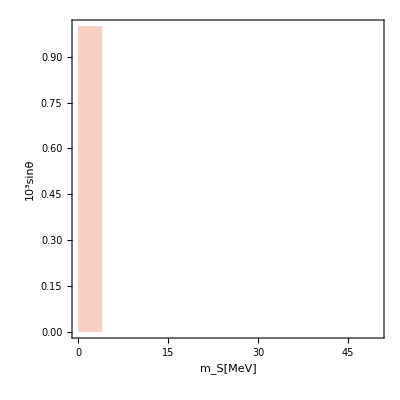

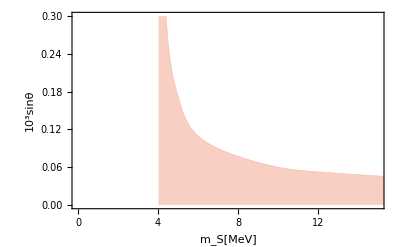

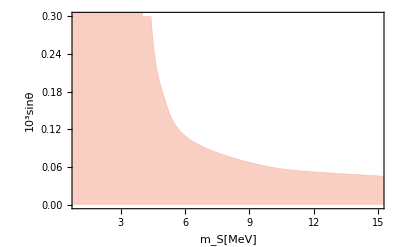

```mathematica
Planckdata={#1,1000#2}&@@@Import[NotebookDirectory[]<>"./Planck.csv"];
Planck01=RegionPlot[mS<=Min[{#1}&@@@Planckdata+0.015],{mS,0,50},{s,0,1.},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S[MeV]",FontFamily->"Times",FontSize->18],Style["10^3sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotRangePadding->None,PlotStyle->{ColorData[97,4],Opacity[0.3]}]//cleanRegionPlot
Planck02=ListLinePlot[Planckdata,PlotRange->{{0,15},{0,0.3}},InterpolationOrder->3,AxesOrigin->{1,0.},Filling->Bottom,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S[MeV]",FontFamily->"Times",FontSize->18],Style["10^3sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotRangePadding->None,PlotStyle->{ColorData[97,4],Opacity[0.3],Thickness[0.001]},FillingStyle->Opacity[0.3]]
Planck=Show[Planck02,Planck01,PlotRange->{{1,15},{0,0.3}}]
```

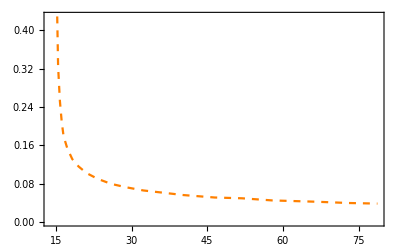

```mathematica
CMBS4data={#1,1000#2}&@@@Import[NotebookDirectory[]<>"CMB-perspective.csv"];
CMBS4=ListLinePlot[CMBS4data,PlotStyle->Directive[Dashed,Orange]]
```

## Combine

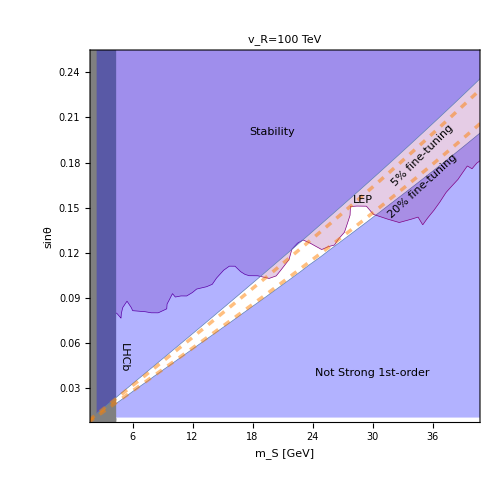

```mathematica
Show[{GeVSFOPTplot‵5,LEP,LHCb,GeVstabilityplot‵5,finetune5},PlotRange->{{2.5,40},{0.012,0.25}},AspectRatio->1,PlotLabel->Style["v_R=100 TeV"],Epilog->{Inset[Framed[Style["LEP",FontFamily->"Times",FontSize->20,Purple],FrameStyle->None],{29,0.155}],Inset[Framed[Style["Not Strong 1st-order", FontSize->20,FontFamily->"Times",Blue],FrameStyle->None],{30,0.04}],Inset[Rotate[Framed[Style["LHCb",Gray,FontSize->20,FontFamily->"Times"],FrameStyle->None],-90 Degree],{5.1,0.05}],Inset[Framed[Style["Stability", FontSize->20,FontFamily->"Times",Blue],FrameStyle->None],{20,0.2}],Inset[Rotate[Framed[Style["5% fine-tuning",Orange],FrameStyle->None],45 Degree],{35,0.185}],Inset[Rotate[Framed[Style["20% fine-tuning",ColorData[97,4]],FrameStyle->None],42.5 Degree],{35,0.164}]}]
```

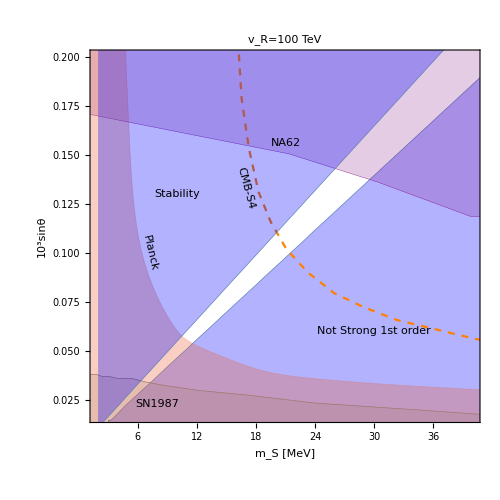

```mathematica
Show[{MeVSFOPTplot‵5,SN,NA62Plot1,Planck,CMBS4,MeVstabilityplot‵5},AspectRatio->1,PlotLabel->Style["v_R=100 TeV"],PlotRange->{{1.9,40},{0.017,0.2}},Epilog->{Inset[Framed[Style["NA62",Purple,FontFamily->"Times",FontSize->20],FrameStyle->None],{21,0.156}],Inset[Framed[Style["SN1987",Gray,FontFamily->"Times",FontSize->20],FrameStyle->None],{8,0.023}],Inset[Framed[Style["Not Strong 1st order",Blue,FontSize->20,FontFamily->"Times"],FrameStyle->None],{30,0.06}],Inset[Rotate[Framed[Style["Planck",ColorData[97,6],FontFamily->"Times",FontSize->20],FrameStyle->None],-77Degree],{7.2,0.1}],Inset[Rotate[Framed[Style["CMB-S4",ColorData[97,6]],FrameStyle->None],-75Degree],{17.,0.133}],Inset[Framed[Style["Stability",Blue,FontSize->20,FontFamily->"Times"],FrameStyle->None],{10,0.13}]}]
```

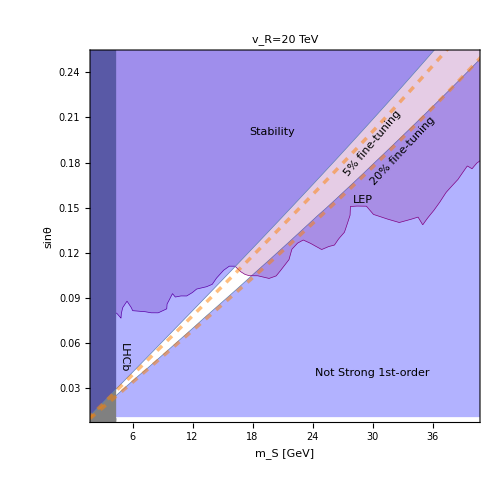

```mathematica
Show[{GeVSFOPTplot‵20,LEP,LHCb,GeVstabilityplot‵20,finetune20},PlotRange->{{2.5,40},{0.012,0.25}},AspectRatio->1,PlotLabel->Style["v_R=20 TeV"],Epilog->{Inset[Framed[Style["LEP",FontFamily->"Times",FontSize->20,Purple],FrameStyle->None],{29,0.155}],Inset[Framed[Style["Not Strong 1st-order", FontSize->20,FontFamily->"Times",Blue],FrameStyle->None],{30,0.04}],Inset[Rotate[Framed[Style["LHCb",Gray,FontSize->20,FontFamily->"Times"],FrameStyle->None],-90 Degree],{5.1,0.05}],Inset[Framed[Style["Stability", FontSize->20,FontFamily->"Times",Blue],FrameStyle->None],{20,0.2}],Inset[Rotate[Framed[Style["5% fine-tuning",Orange],FrameStyle->None],50 Degree],{30,0.193}],Inset[Rotate[Framed[Style["20% fine-tuning",ColorData[97,4]],FrameStyle->None],47 Degree],{33,0.188}]}]
```

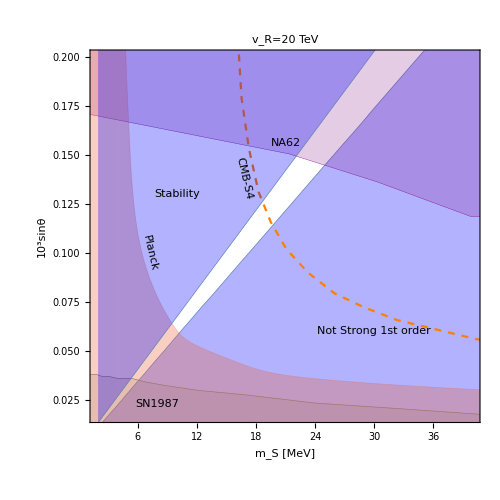

```mathematica
Show[{MeVSFOPTplot‵20,SN,NA62Plot1,Planck,CMBS4,MeVstabilityplot‵20},AspectRatio->1,PlotLabel->Style["v_R=20 TeV"],PlotRange->{{1.9,40},{0.017,0.2}},Epilog->{Inset[Framed[Style["NA62",Purple,FontFamily->"Times",FontSize->20],FrameStyle->None],{21,0.156}],Inset[Framed[Style["SN1987",Gray,FontFamily->"Times",FontSize->20],FrameStyle->None],{8,0.023}],Inset[Framed[Style["Not Strong 1st order",Blue,FontSize->20,FontFamily->"Times"],FrameStyle->None],{30,0.06}],Inset[Rotate[Framed[Style["Planck",ColorData[97,6],FontFamily->"Times",FontSize->20],FrameStyle->None],-77Degree],{7.2,0.1}],Inset[Rotate[Framed[Style["CMB-S4",ColorData[97,6]],FrameStyle->None],-77 Degree],{16.8,0.138}],Inset[Framed[Style["Stability",Blue,FontSize->20,FontFamily->"Times"],FrameStyle->None],{10,0.13}]}]
```